# APPM 2350 Project #2

### By Davis Landry, Mahalie Hill, Mia Miller

## 3 Defining the Mountain Range

```mathematica
mR = {{{1,1},1,.9,"K-13"},{{3,1},3,1,"Mount Adamore"},{{3.75,1},2,.8,"Issaquah Peak"},{{4,3},2,1,"Mount Jojo"},{{3,3.5},3,.75,"Soweroski Peak"},{{2,3},2,.9,"Leibs Peak"},{{.75,3},4,.5,"Jacobi Peak"}};

gaussian[ϵ_,r_] = E^(-(ϵ*r)^2);
m[x_,y_] := Sum[mR[[i,3]]* gaussian[mR[[i,2]],Sqrt[(Sqrt[(mR[[i,1,1]]-x)^2 + (mR[[i,1,2]]-y)^2])^2]],{i,7}];
mountainLabels = Table[Graphics[{White, Text[mR[[i,4]],mR[[i,1]]]}],{i,7}];
mountainLabels3D = Table[Graphics3D[{White,Text[mR[[i,4]],{mR[[i,1,1]],mR[[i,1,2]],m[mR[[i,1,1]],mR[[i,1,2]]]}]}],{i,7}];

mountainPlot3D = Plot3D[m[x,y],{x,0,5},{y,0,5}, AxesLabel->{"x in 1000ft","y in 1000ft","From 7000ft in 1000ft"}, PlotLabel->"Lagrange Mountain Range", ColorFunction->"GreenBrownTerrain"];

mountainContour = ContourPlot[m[x,y],{x,0,5},{y,0,5}, PlotLegends->Automatic, ColorFunction->"Rainbow",Frame->{True,True,False,False},
PlotLabel->"Lagrange Mountain Range Contour", Contours->20, FrameLabel->{"x in 1000ft","y in 1000ft"}];
```

## 4 Analyzing the Mountain Range

Plotting Paths

-Graphics3D-

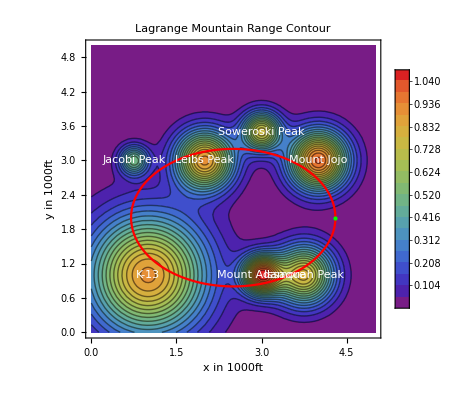

```mathematica
mt[t_] :=Sum[mR[[i,3]]* gaussian[mR[[i,2]],Sqrt[(Sqrt[(mR[[i,1,1]]-(2.5 + 1.8Cos[4t]))^2 + (mR[[i,1,2]]-(2+1.2Sin[4t]))^2])^2]],{i,7}];

r[t_] = {2.5 + 1.8Cos[4t], 2+1.2Sin[4t]};
r3D[t_] := {2.5 + 1.8Cos[4t], 2+1.2Sin[4t],mt[t]};

path3D = ParametricPlot3D[r3D[t],{t,0,π/2}, PlotStyle->{Red,Thickness[.01]}];
path = ParametricPlot[r[t],{t,0,π/2}, PlotStyle->Red];

point3D = Graphics3D[{PointSize[Large],Green,Point[r3D[0]]}];
point = Graphics[{PointSize[Large],Green,Point[r[0]]}];

Show[{mountainPlot3D  ,path3D,point3D, mountainLabels3D}]
Show[{mountainContour,path    ,point, mountainLabels}]
```

Honey Badger

```mathematica
gradM[x_,y_] = Grad[m[x,y],{x,y}];
(* a = Table[Graphics3D[Arrow[Tube[{r3D[t],r3D[t]+gradr3D[t]}]]],{t,0,π/2,π/30}];
Show[{mountainPlot3D  ,path3D,point3D,a}] 
*)

Dot[gradM[2.5 + 1.8Cos[π], 2+1.2Sin[π]],Normalize[r'[π/4]]]
mt'[π/4]
```

0.605035

2.90417

Change of Elevation

{14.7402,{t→1.22109}}

{-8.97206,{t→0.51835}}

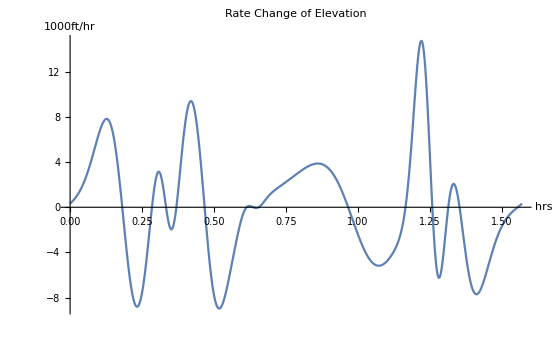

```mathematica
Maximize[{mt'[t],t>= 0},t]
Minimize[{mt'[t],0<=t<= π/2},t]
Plot[mt'[t],{t,0,π/2},PlotLabel->"Rate Change of Elevation",AxesLabel->{"hrs","1000ft/hr"}]
```

```mathematica
1.221086074164095*60
0.5183504795465874*60
```

73.2652

31.101

Highest Elevation

```mathematica
gradMount[x_,y_] := {16. E^(-16 ((0.75 -x)^2+(3-y)^2)) (0.75 -x)+1.8 E^(-(1-x)^2-(1-y)^2) (1-x)+7.2E^(-4 ((2-x)^2+(3-y)^2)) (2-x)+18 E^(-9 ((3-x)^2+(1-y)^2)) (3-x)+13.5 E^(-9 ((3-x)^2+(3.5-y)^2)) (3-x)+6.4 E^(-4 ((3.75-x)^2+(1-y)^2)) (3.75-x)+8 E^(-4 ((4-x)^2+(3-y)^2)) (4-x),1.8 E^(-(1-x)^2-(1-y)^2) (1-y)+18 E^(-9 ((3-x)^2+(1-y)^2)) (1-y)+6.4 E^(-4 ((3.75-x)^2+(1-y)^2)) (1-y)+16. E^(-16 ((0.75-x)^2+(3-y)^2)) (3-y)+7.2 E^(-4 ((2-x)^2+(3-y)^2)) (3-y)+8 E^(-4 ((4-x)^2+(3-y)^2)) (3-y)+13.5 E^(-9 ((3-x)^2+(3.5-y)^2)) (3.5 -y)};
carR[x_,y_] := (x-2.5)^2/3.24+(y-2)^2/1.44;
gradR[x_,y_] := {0.6172839506172839 (-2.5+x),1.3888888888888888 (-2+y)};

FindRoot[{gradMount[x,y] == λ*gradR[x,y],carR[x,y]== 1},{{λ,-1},{x,3},{y,1}}]

(*Plot[mt[t],{t,0,π/2}]*)
m[3.074084653389694,0.8626684621463107]
```

{λ→-1.34201,x→3.07408,y→0.862668}

0.934484

Thus the highest point is at 7934 ft above sea level.

Lake Mochi

{x→3.08489,y→2.1327}

-Graphics3D-

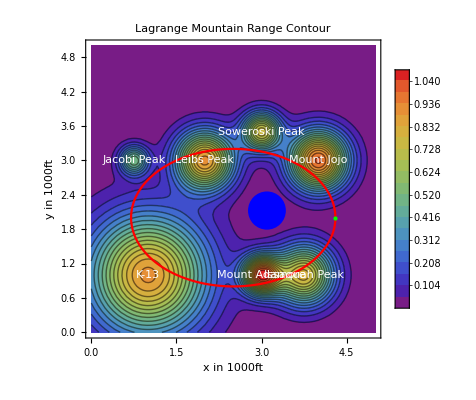

```mathematica
FindRoot[gradMount[x,y]==0 ,{{x,3},{y,2}}]

mochi = Graphics[{Blue,Disk[{3.084891978358271,2.1326960054211934},1/3]}];
mochi3D = Graphics3D[{Blue,Cylinder[{{3.084891978358271,2.1326960054211934,0},{3.084891978358271,2.1326960054211934,0.025}},2/3]}];

Show[{mountainPlot3D  ,path3D,point3D, mochi3D, mountainLabels3D}]
Show[{mountainContour,path    ,point  , mochi, mountainLabels}]
```

Rock inside of trail

```mathematica
NIntegrate[1,{x,0.7,4.3},{y,0.06666666666666667 (30. -1. Sqrt[-301.+500. x-100. x^2]),0.06666666666666667(30.+Sqrt[-301.+500. x-100. x^2])},{z,-7,m[x,y]}]*1000^3
```

4.9366×10^10

Clairautnium

```mathematica
delta[x_,y_,z_] := E^(-.25((x-2.5)^2+(y-2.5)^2+(z-.2)^2));
NIntegrate[delta[x,y,z],{x,0,5},{y,0,5},{z,0,m[x,y]}]*1000^-3
```

2.51448×10^-9

For Intro

```mathematica
delta[x_,y_,z_] := E^(-.25((x-2.5)^2+(y-2.5)^2+(z-.2)^2));
NIntegrate[delta[x,y,z],{x,0,5},{y,0,5},{z,0,m[x,y]}]
ArcLength[r3D[t],{t,0,π/2}]
```

2.51448

11.8138

```mathematica
NIntegrate[Abs[mt'[t]],{t,0,π/2}]*1000
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.31613}. NIntegrate obtained 6.03268 and 0.000115168 for the integral and error estimates.

6032.68

EC

```mathematica
(* All of the Radial Functions *)
aussian[a_,r_] := ⅇ^(-(a*r)^2);
multiquadric[a_,r_] := Sqrt[1+(a*r)^2];
inverseQuadratic[a_,r_] := 1/(1+(a*r)^2);
inverseMultiquadric[a_,r_] := 1/Sqrt[1+(a*r)^2];

gau[l_,a_,x_,y_,xBar_,yBar_]    := l * aussian[a,Sqrt[(Sqrt[(xBar-x)^2 + (yBar-y)^2])^2]];
invM[l_,a_,x_,y_,xBar_,yBar_]  := l * inverseMultiquadric[a,Sqrt[(Sqrt[(xBar-x)^2 + (yBar-y)^2])^2]];
mult[l_,a_,x_,y_,xBar_,yBar_]  := l * multiquadric[a,Sqrt[(Sqrt[(xBar-x)^2 + (yBar-y)^2])^2]];invQ [l_,a_,x_,y_,xBar_,yBar_]:= l *inverseQuadratic[a,Sqrt[(Sqrt[(xBar-x)^2 + (yBar-y)^2])^2]];

funcTable[i_,l_,a_,x_,y_,xBar_,yBar_] := Switch[i,1,gau[l,a,x,y,xBar,yBar],2,invQ[l,a,x,y,xBar,yBar],3,invM[l,a,x,y,xBar,yBar],4,mult[l,a,x,y,xBar,yBar]];

(*
List of point {{xMiddle,yMiddle},{epsilon},{lambda},{plot function}}}
plot function:
1:gaussian
2:inverseQuadratic
3:inverseMultiquadric
4:multiquadric
*)

ecMount = Table[Table[{{Random[Real,{0,5},3],Random[Real,{0,5},3]},Random[Real,{1,5},3],Random[Real,{-.5,3},3],Random[Integer,{1,3}]},{k,Random[Integer,{10,40}]}],{m,50}];

ecM[x_,y_,j_] := Sum[funcTable[ecMount[[j,i,4]],ecMount[[j,i,3]],ecMount[[j,i,2]],x,y,ecMount[[j,i,1,1]],ecMount[[j,i,1,2]]],{i,Length[ecMount[[j]]]}];

allPlots = Table[Plot3D[ecM[x,y,n],{x,0,5},{y,0,5},PlotRange->All,ColorFunction->"GreenBrownTerrain"],{n,50}]
```

General::munfl: Exp[-931.827] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-762.583] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-743.236] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}